# Predict Scale of Satellite Images

Some explanation

Mehmet Sahin, Jun. 26,  2018

Some explanation

## Collect Satellite Images

In this section, we will get the data using GeoImage.

Some explanation

Create a function to getImages from GeoImage:

```mathematica
ClearAll["Global`*"]
```

```mathematica
getImage[coords_List, range_] := 
  	GeoImage[GeoPosition[coords], GeoRange ->range ];
```

Before we create our store image function, we should create a hash function to get unique names for images:

```mathematica
hash[expr_] := 
	IntegerString[Hash[expr],36];
```

Now, let’s create our storeImage function:

```mathematica
imageLocation[image_Image,range_] := 
	FileNameJoin[{NotebookDirectory[],ToString[range]<>"-"<>hash[image]<>".png"}];
```

Give it a try:

```mathematica
imageLocation[getImage[{40.6642738,-73.9385004},1],1]
```

/Users/mehmetsahin/Documents/GitHub/Summer2018Starter/Project/Predict Scale of Satellite Images/1-4hbid8lnxwml.png

Create a function to get countries’ geo positions randomly:

```mathematica
geoPositionOfCountry[entities_,numberOfPosition_Integer,folderName_String] :=
	Module[{},
	countries = entities;
	mesh = DiscretizeGraphics@EntityValue[countries,"Polygon"];
	SeedRandom[Hash@{folderName,countries}];
	Reverse[RandomPoint[mesh,numberOfPosition],{2}]
]
```

Let’s plot them and see how those random positions act on a Graphic

```mathematica
data = geoPositionOfCountry[{Entity["Country","Turkey"],Entity["Country","Italy"],Entity["Country","India"]},600,"training"];
GeoListPlot@GeoPosition@data;
```

```mathematica
getZoomLevel[point_] := 
	(SeedRandom[Hash[point]]; normalize[RandomReal[]]);
```

```mathematica
SetAttributes[{getGeoRange, normalize}, Listable]

(*getGeoRange[zoom_] := zoom * Quantity[8800,"Miles"] + Quantity[0.2,"Miles"];*)
getGeoRange[zoom_] := zoom * 8800 + 0.2
normalize[number_] := If[number<0.3,number,number^11];
(*ImagePartition[GeoImage[Entity["Country","Italy"], GeoRange->getGeoRange[1],ImageSize->800],{100}] // Grid;*)
```

```mathematica
data = geoPositionOfCountry[{Entity["Country","Turkey"],Entity["Country","Italy"],Entity["Country","India"]},10000,"training"];
zoomLevel = getZoomLevel[#]&/@data;
geoRange = getGeoRange@getZoomLevel[#]&/@data;
```

Check the distribution of points and zoom level:

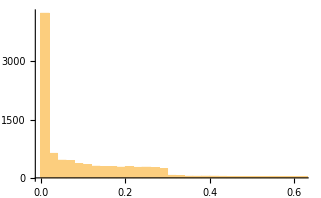

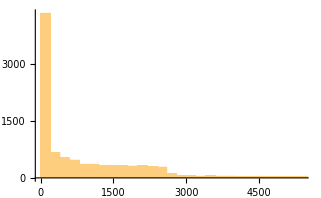

0.215659

-Graphics-

0.0539147

-Graphics-

```mathematica
Histogram@zoomLevel
Histogram@geoRange
Min[geoRange]
GeoImage[Entity["City",{"Rome","Lazio","Italy"}],GeoRange->Quantity[Min[geoRange],"Miles"],ImageSize->Medium]
Min[geoRange]/4
GeoImage[Entity["City",{"Rome","Lazio","Italy"}],GeoRange->Quantity[Min[geoRange]/4,"Miles"],ImageSize->Medium]
```

Create a function to return a association of points and zoom level:

```mathematica
createTheDataSet[points_List] := 
	Map[<|"Point"->#,"Zoom"->getZoomLevel[#]|>&,points];
```

Call the createTheDataSet function:

```mathematica
assocoatedData = createTheDataSet[data];
```

```mathematica
Take[assocoatedData,3]
Take[Dataset@assocoatedData,3]
```

{<|Point→{36.9393,37.0554},Zoom→0.000609432|>,<|Point→{18.7333,76.0088},Zoom→0.0408344|>,<|Point→{38.6824,37.3229},Zoom→0.136202|>}

Dataset[<>]

Let’s now write our function that will encode and decode name of the images:

```mathematica
encodeID[expr_]:=StringReplace[Developer`EncodeBase64@BinarySerialize@expr,"/"->"~"]
decodeID[expr_]:=BinaryDeserialize@Developer`DecodeBase64ToByteArray@StringReplace[expr,"~"->"/"]
```

Try out the encodeID and decodeID:

```mathematica
encodeID[Take[assocoatedData,{4}]]
```

ODpmAXMETGlzdEECLVMFUG9pbnTBIwECYoS0ZfVnRECGQjS3kfhBQC1TBFpvb21yACBw5Uvfhz8=

```mathematica
decodeID[%]
```

{<|Point→{40.8122,35.9419},Zoom→0.0116564|>}

## Section 2

In the last section ..

## Section 3

Now ..

## Conclusion

## Author contact information

Mehmet Sahin

6/28/2018
mehmetmshin@gmail.com

## Further Work

Mehmet Sahin

6/28/2018
mehmetmshin@gmail.com